Type II & Type III Oscillations

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Place relevant file string for Dynamica here *)
Quiet[<<".../Dynamica.m"]
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## SYSTEMS

## T2 AS

### F2A, A1A

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k1]
```

```mathematica
T2AS = DynamicalSystem[{
e*(f/(h+A))*A*S - ds*S ,
r*A*(1 - A/k1)-(f/(h+A))*A*S
},
{{S,0,200},{A,0,10}},
{{e,0,1000},{h,0,1},{f,0,1},{ds,0.001,0.14},{r,0,2},{k1,0.01,6}}]
```

DynamicalSystem[«2 ODEs»,{S,A},{e,h,f,ds,r,k1}]

```mathematica
T2AS = T2AS/.{e->8,h -> 0.2314, f->0.0153,  r->1}
```

DynamicalSystem[«2 ODEs»,{S,A},{ds,k1},{e→8,f→0.0153,h→0.2314,r→1}]

Warning: A convergence failure occurred during continuation

Warning: A convergence failure occurred during continuation

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,A,k1,ds}={0,0.01,0.01,0.00507042253521127}

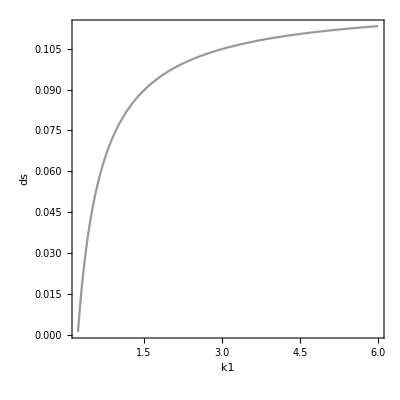

```mathematica
PCT2AS = DisplayParameterChart[T2AS,{k1,ds},MaxStepSize->0.01,MaxSteps->Infinity, PlotRange->All]
```

#### Sin

```mathematica
dAT2AS = r*A*(1 - A/k1)-(f/(h+A))*A*S;
dST2AS= e*(f/(h+A))*A*S - ds*S ;
```

Get Boundary S & A to plug into Sin

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
r = 1;
```

```mathematica
S0SA= (e*(f/(h+k1))*k1)/ds;
```

```mathematica
S0SA/.{ds->0.12075,k1->2}
```

0.908546

#### Construct Chart

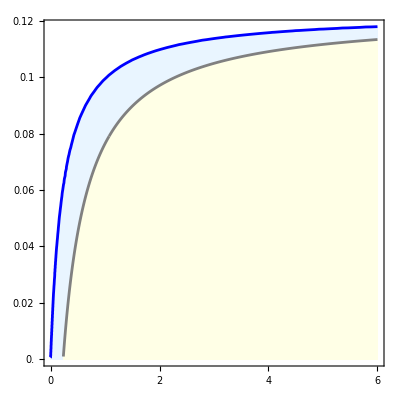

```mathematica
FCT2AS = Show[PCT2AS,
RegionPlot[S0SA>=1 ,{k1,0,6},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[LightBlue]],
ListLinePlot[PCT2AS[[1]][[1]][[1]][[3]][[1]],PlotStyle->Gray,Filling->Bottom,FillingStyle->Lighter[Yellow,0.9], PlotRange->All],
ContourPlot[S0SA==1,{k1,0,6},{ds,0,0.14},ContourStyle->{Blue,Thickness->0.005}],
(*FrameLabel->{"Carrying Capacity (K)","Host Death Rate (d_S)"},*)
FrameTicks->{{{0.00,0.02,0.04,0.06,0.08,0.10,0.12},None},{{0,1,2,3,4,5,6},None}},FrameLabel->None,LabelStyle->{Black,16}, PlotRange->{{0,6},All}]
```

#### Time Series

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
r = 1;
```

```mathematica
Clear[ds,k1]
ds = 0.06;
ParaT2AS=ParametricNDSolveValue[{S'[t]== e*(f/(h+A[t]))*S[t]*A[t] - ds*S[t] ,
A'[t] == r*A[t]*(1 - A[t]/k1)-(f/(h+A[t]))*A[t]*S[t],
S[0]==11.17, A[0]==0.325},{S,A},{t,0,6000},{k1}];
```

```mathematica
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@ParaT2AS[k1]],{t,0,5500},PlotRange->{{100,500},{0.000005,500}},
 PlotStyle->{{Blue,Thick},{Darker[Green],Thick}},
PlotLegends->{"Susceptible","Algae"},TicksStyle->10,AspectRatio->1, LabelStyle->16, Frame->True, FrameLabel->{"Time","Log Concentration"}, FrameStyle->Black]],
{{k1,2.5},1,8}]
```

### A1C

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k1]
```

```mathematica
T2AS = DynamicalSystem[{
e*(f/(h+A))*A*S - ds*S ,
r*A*(1 - A/k1)-(f/(h+A))*A*S
},
{{S,0,200},{A,-0.1,10}},
{{e,0,1000},{h,0,1},{f,0,1},{ds,0.001,0.14},{r,0,2},{k1,0.01,6}}]
```

DynamicalSystem[«2 ODEs»,{S,A},{e,h,f,ds,r,k1}]

```mathematica
T2AS = T2AS/.{e->8,h -> 0.2314, f->0.0153,  r->1}
```

DynamicalSystem[«2 ODEs»,{S,A},{ds,k1},{e→8,f→0.0153,h→0.2314,r→1}]

```mathematica
traj = DisplayTrajectories[T2AS/.{k1->2,ds->0.1},{{44.1484,0.0001}},140, StateVariables->{A,S}, MaxSteps->Infinity, PlotRange->{{0,All},{0,All}}, PlotStyle->{Blue,Thickness[0.018]},FrameLabel->None];
```

```mathematica
Last[First[$Trajectories]]
```

{22.2441,9.8824×10^-11}

```mathematica
dAT2AS = r*A*(1 - A/k1)-(f/(h+A))*A*S;
dST2AS= e*(f/(h+A))*A*S - ds*S ;
```

```mathematica
solsT2AS = Solve[{dAT2AS==0,dST2AS==0},{A,S},WorkingPrecision->MachinePrecision];
```

```mathematica
solsT2AS
```

{{A→-(ds h)/(ds-e f),S→(e h (-ds h-ds k1+e f k1) r)/((ds-e f)^2 k1)},{A→k1,S→0},{A→0.,S→0.}}

```mathematica
Solve[dST2AS==0,A]
```

{{A→-(ds h)/(ds-e f)}}

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
r = 1;
k1 = 2;
ds = 0.1;
```

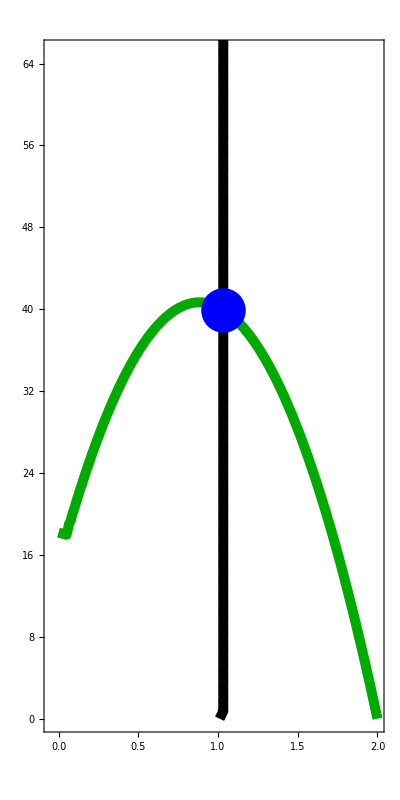

```mathematica
Show[
(*traj,*)
ContourPlot[dAT2AS==0,{A,0,10},{S,0,150}, PlotPoints->100, ContourStyle->{Darker[Green],Thickness[0.018]}],
ContourPlot[dST2AS==0,{A,0,10},{S,0,150}, PlotPoints->100, ContourStyle->{Black,Thickness[0.018]}],
Graphics[{PointSize->0.08,Blue,Point[{solsT2AS[[1]][[1]][[2]],solsT2AS[[1]][[2]][[2]]}]}],
PlotRange->{{-0.05,2},{0,65}},AspectRatio->2,LabelStyle->{Black,16}
]
```

```mathematica
dST2AS
```

(0.1224 A S)/(0.2314+A)-ds S

### A1E

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k]
```

```mathematica
dAT2AS = r*A*(1 - A/k1)-(f/(h+A))*A*S;
dST2AS= e*(f/(h+A))*A*S - ds*S ;
```

```mathematica
solsT2AS = Solve[{dAT2AS==0,dST2AS==0},{A,S},WorkingPrecision->MachinePrecision];
```

```mathematica
solsT2AS[[1]]
```

{A→-(ds h)/(ds-e f),S→(e h (-ds h-ds k1+e f k1) r)/((ds-e f)^2 k1)}

```mathematica
AstarT2AS:=-(ds h)/(ds-e f)
SstarT2AS := (e h (-2 ds+2 e f-ds h) r)/(2 (ds-e f)^2)
```

```mathematica
(*Clear[k1];*)
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
k1 = 2;
```

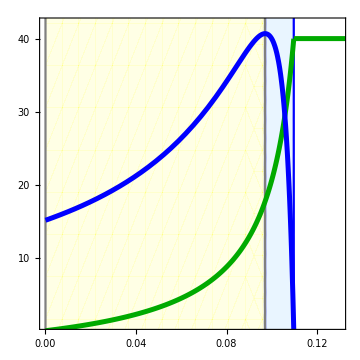

```mathematica
P2 = Show[
RegionPlot[0.1097 > x>0.097,{x,0,0.14},{y,0,100}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[0.097 > x,{x,0,0.14},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
Plot[k1*20,{ds,0.1097,0.15}, PlotStyle->{Darker[Green], Thickness[0.01]}],
Plot[AstarT2AS*20,{ds,0,0.1097}, PlotPoints->1000,PlotStyle->{Darker[Green],Thickness[0.01]}],
Plot[SstarT2AS,{ds,0,0.16}, PlotStyle->{Blue,Thickness[0.01]}],
PlotRange->{{0,0.13},{1,42}},
FrameTicks->{{{0,10,20,30,40},None},{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"},0.12,0.14},None}},
Frame->True, AspectRatio->1,LabelStyle->{Black,16},ImageSize->Medium
]
```

### A1G

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k1]
```

```mathematica
J11T2AS = FullSimplify[D[dAT2AS/A,A]]
```

-r/k1+(f S)/(A+h)^2

```mathematica
Clear[ds]
SelfLimT2AS = -r/k1;
ClearanceT2AS = (f SstarT2AS)/(AstarT2AS+h)^2;
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
k1=2;
```

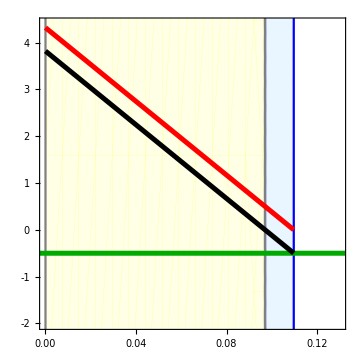

```mathematica
P4 = Show[
RegionPlot[0.1097 > x>0.097,{x,0,0.14},{y,-10,10}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[0.097 > x,{x,0,0.14},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
Plot[SelfLimT2AS,{ds,-1,0.15}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[ClearanceT2AS,{ds,0,0.1097 }, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[SelfLimT2AS + ClearanceT2AS,{ds,0,0.1097 }, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,0.13},{-2,4.4}},AxesOrigin->{0,0},Axes->True,
FrameTicks->{{{-2,-1,0,1,2,3,4},None},{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"},0.12,0.14},None}},
Frame->True,FrameLabel->{"Host Death Rate (d_s)"}, LabelStyle->{Black,16},ImageSize->Medium
]
```

## T2 ASI

### F2B, A1B, A3A

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k1]
```

```mathematica
T2ASI = DynamicalSystem[{
r*A*(1 - A/k1)-(f/(h+A))*A*(S+theta*F),
e*(f/(h+A))*(S+theta*F)*A - ds*S - u*S*F,
u*S*F - (ds + v)*F
},
{{A,0,10},{S,0,200},{F,-0.01,200}},
{{e,0,1000},{h,0,1},{f,0,1},{ds,0.001,0.14},{u,0,2},{v,0,0.2},{theta,0,1},{r,0,2},{k1,0.01,6}}]
```

DynamicalSystem[«3 ODEs»,{A,S,F},{e,h,f,ds,u,v,theta,r,k1}]

```mathematica
T2ASI = T2ASI/.{e->8,h -> 0.2314, f->0.0153, u->0.0075, v->0.05157, theta->0.8, r->1}
```

DynamicalSystem[«3 ODEs»,{A,S,F},{ds,k1},{e→8,f→0.0153,h→0.2314,r→1,theta→0.8,u→0.0075,v→0.05157}]

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.006;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

General::munfl: 0.-1.07406137944502×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.-3.86808982034535×10^-321 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.+2.1122294491005×10^-319 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Warning: A convergence failure occurred during continuation

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,S,F,k1,ds}={0.00531878439655663,7.24269063493665,0,0.01,0.00275017976202484}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,S,F,k1,ds}={0.01,0,0,0.01,0.00507042253521127}

Warning: A convergence failure occurred during continuation

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,S,F,k1,ds}={5.64784123005208,22.5536640501335,0,6,0.117582480376001}

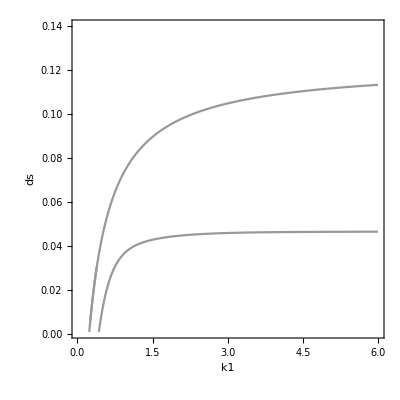

```mathematica
PCT2ASI = DisplayParameterChart[T2ASI,{k1,ds},MaxSteps->Infinity, MaxStepSize->0.12]
```

#### R0 & Sin

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k1]
```

```mathematica
dAT2ASI=r*A*(1 - A/k1)-(f/(h+A))*A*(S+theta*F);
dST2ASI=e*(f/(h+A))*A *(S+theta*F)- ds*S - u*S*F;
dFT2ASI=u*S*F - (ds + v)*F;
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 0.0075;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

```mathematica
solsT2ASI=Solve[{dST2ASI==0,dFT2ASI==0,dAT2ASI==0},{S,F,A}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsT2ASI[[1]]/.{ds->0.035,k1->1}
```

{S→19.218,F→0.,A→0.0926659}

Get Boundary S & A to plug into R0

```mathematica
SatBT2ASI=solsT2ASI[[1,1,2]];
AatBT2ASI=solsT2ASI[[1,3,2]];
```

R0 Equation

```mathematica
R0T2ASI= (u*SatBT2ASI)/(ds+v);
```

```mathematica
S0T2ASI = (e*(f/(h+k1))*k1)/ds;
```

#### R0 on cycles - R0 average (FA2A)

```mathematica
Clear[k1,k,d,ds, r0, r0current,stest,a,i,j];
```

```mathematica
R0CYCT2[k0_,ds0_]:=
Module[{k=k0, d = ds0},
(* Equilibrate *)
DisplayTrajectories[T2ASI/.{k1->k,ds->d},{{2,15,0}},5000, StateVariables->{A,S}, MaxSteps->Infinity,MaxStepSize->0.01];
(* R0 *)
DisplayTrajectories[T2ASI/.{k1->k,ds->d},{{Last[First[$Trajectories]][[1]],Last[First[$Trajectories]][[2]],0}},5000, StateVariables->{A,S}, MaxIterations->Infinity,MaxSteps->Infinity,MaxStepSize->0.01];
r0 = 0;
For[a=1,a<=Length[$Trajectories[[1]]],a++,
stest = $Trajectories[[1]][[a]][[2]];
r0current = (u*stest)/(d+v);
r0 = r0 + r0current;
];
r0 = r0/Length[$Trajectories[[1]]];
r0
]
```

```mathematica
granK = 0.025; (* 0.025 *)
granDS = 0.001; (* 0.0005 *)
startK = 0.2;
startDS = 0.01;
maxK = 6;
maxDS = 0.115; (* 0.115 *)
```

```mathematica
R0cycdataT2 = {};
For[i=(startK/granK),i<=(maxK/granK),i++,
Clear[k];
k = i * granK;
For[j=(startDS/granDS),j<=(maxDS/granDS),j++,
Clear[d];
d = j * granDS;
AppendTo[R0cycdataT2,{k, d,R0CYCT2[k,d]}];
]
]
```

General::munfl: (-2.05538×10^-243)^2 is too small to represent as a normalized machine number; precision may be lost.

```mathematica
Export["R0cycleT2.dat",R0cycdataT2];
```

```mathematica
R0cycdataT2=Import["R0cycleT2.dat","Table"];
```

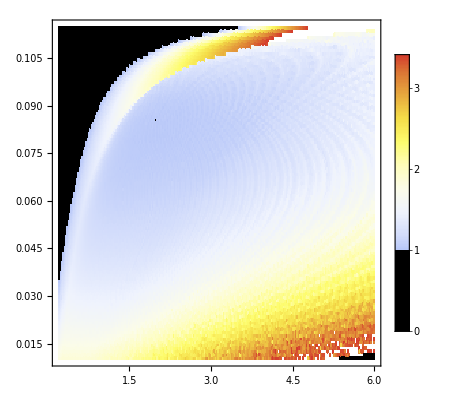

```mathematica
R0cycplotT2 =ListDensityPlot[Transpose[ArrayReshape[R0cycdataT2[[All,3]],{IntegerPart[(maxK/granK) - (startK/granK)+1],IntegerPart[(maxDS/granDS)-(startDS/granDS)+1]}]],DataRange->{{startK,maxK},{startDS,maxDS}},ColorFunction->(If[#<1,Black,ColorData["TemperatureMap",#/3.5]]&),ColorFunctionScaling->False,
InterpolationOrder->0, PlotLegends->Automatic]
```

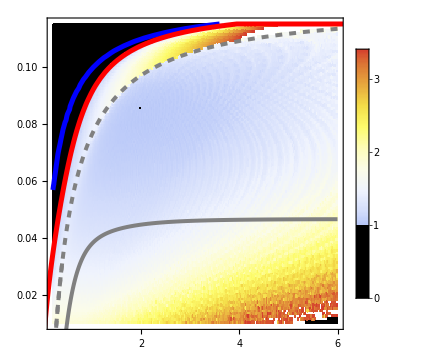

```mathematica
R0PT2ASI= Show[
R0cycplotT2 ,
ListLinePlot[PCT2ASI[[1]][[1]][[1]][[3]][[1]],PlotStyle->{Gray, Thickness->0.008,Dashed},PlotRange->All],
ListLinePlot[PCT2ASI[[1]][[1]][[2]][[3]][[1]],PlotStyle->{Gray, Thickness->0.008,Dashed},PlotRange->All],

ListLinePlot[PCT2ASI[[1]][[1]][[3]][[3]][[1]],PlotStyle->{Gray,Thickness->0.008},PlotRange->All],

ContourPlot[S0T2ASI==1,{k1,startK,maxK},{ds,startDS,maxDS},ContourStyle->{Blue,Thickness->0.01}],
RegionPlot[R0T2ASI>=1 ,{k1,0,7},{ds,-0.1,maxDS}, BoundaryStyle->{Red,Thickness->0.01},PlotStyle->Opacity[0.0]],

ImageSize->Medium,
FrameTicks->{{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"}, 0.12},None},{{0,1,2,3,4,5,6},None}},
LabelStyle->{16,Black},AxesOrigin->{0,0},
AspectRatio->1,PlotRange->{{startK,maxK},{startDS,maxDS}}, PlotRangeClipping->True
]
```

#### Construct Chart

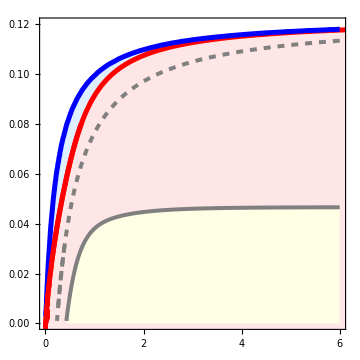

```mathematica
FCT2ASI= Show[
RegionPlot[S0T2ASI>=1 ,{k1,0,6},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->LightBlue],
RegionPlot[R0T2ASI>=1 ,{k1,0,7},{ds,-0.1,0.14}, BoundaryStyle->{Red,Thickness->0.01},PlotStyle->Lighter[Red,0.9]],

ListLinePlot[PCT2ASI[[1]][[1]][[1]][[3]][[1]],PlotStyle->{Gray, Thickness->0.008,Dashed},PlotRange->All],
ListLinePlot[PCT2ASI[[1]][[1]][[2]][[3]][[1]],PlotStyle->{Gray, Thickness->0.008,Dashed},PlotRange->All],

ListLinePlot[PCT2ASI[[1]][[1]][[3]][[3]][[1]],PlotStyle->{Gray,Thickness->0.008},Filling->Bottom,FillingStyle->Lighter[Yellow,0.9],PlotRange->All],


ContourPlot[S0T2ASI==1,{k1,0.001,6},{ds,0.00001,0.14},ContourStyle->{Blue,Thickness->0.01}],
ContourPlot[R0T2ASI==1,{k1,0.001,5},{ds,0.00001,0.08},ContourStyle->{Red,Thickness->0.01}],

ImageSize->Medium,
FrameTicks->{{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"}, 0.12},None},{{0,1,2,3,4,5,6},None}},
LabelStyle->{16,Black},AxesOrigin->{0,0},
AspectRatio->1,PlotRange->{{0,6},{0,0.12}}, PlotRangeClipping->True
]
```

#### Time Series

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 0.8;
r = 1;
```

```mathematica
Clear[ds,k1]
ds = 0.03;
ParaT2ASI=ParametricNDSolveValue[
{S'[t]== e*(f/(h+A[t]))*(S[t]+theta *F[t])*A[t] - ds*S[t] - u*S[t]*F[t],
F'[t] == u*S[t]*F[t] - (ds + v)*F[t],
A'[t] == r*A[t]*(1 - A[t]/k1)-(f/(h+A[t]))*A[t]*(S[t]+theta *F[t]),
S[0]==11.17,F[0]==1, A[0]==0.325},{S,F,A},{t,0,6000},{k1}];
```

```mathematica
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@ParaT2ASI[k1]],{t,0,10000},MaxRecursion->10,PlotRange->{{100,300},{0.00001,100}},
 PlotStyle->{{Blue,Thick},{Red,Thick},{Darker[Green],Thick}},
PlotLegends->{"Susceptible","Infected","Algae"},TicksStyle->10,AspectRatio->1, LabelStyle->16, Frame->True, FrameLabel->{"Time","Log Concentration"}, FrameStyle->Black]],
{{k1,2},0,6}]
```

### A1D

```mathematica
Clear[e,h,f,dh,u,v,theta,r,k1,p]
```

```mathematica
T2AHp = DynamicalSystem[{
r*A*(1 - A/k1)-H*f((1-p)+theta p)(A/(h+A)),
e*f((1-p)+theta p)(A/(h+A))*H - (dh+p v)*H  ,
p ((u H-v) (1-p)-e f((1-p)+theta p)(A/(h+A)))
},
{{A,-0.01,10},{H,-0.01,100}, {p,0,1}},
{{e,0,1000},{h,0,1},{f,0,1},{dh,0.001,0.14},{u,0,2},{v,0,0.2},{theta,0,1},{r,0,2},{k1,0.01,6}}];
```

```mathematica
T2AHp = T2AHp/.{e -> 8, h->0.2314, f->0.0153, u->0.0075, v -> 0.05157, theta->0.8, r->1}
```

DynamicalSystem[«3 ODEs»,{A,H,p},{dh,k1},{e→8,f→0.0153,h→0.2314,r→1,theta→0.8,u→0.0075,v→0.05157}]

```mathematica
traj = DisplayTrajectories[T2AHp/.{k1->2,dh->0.08},{{0.00000001,4.9450,0.92362}},200, StateVariables->{A,H}, MaxSteps->Infinity,MaxStepSize->0.01, PlotRange->{{0,All},{0,All}}, PlotStyle->{Blue,Thickness[0.018]},FrameLabel->None];
```

```mathematica
Last[First[$Trajectories]]
```

{0.703885,47.663,4.53523×10^-7}

```mathematica
dAT2AHp = r*A*(1 - A/k1)-H*f((1-p)+theta p)(A/(h+A));
dHT2AHp = e*f((1-p)+theta p)(A/(h+A))*H - (dh+p v)*H ;
dpT2AHp=p ((u H-v) (1-p)-e f((1-p)+theta p)(A/(h+A)));
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 0.8;
r = 1;
k1=2;
dh = 0.08;
```

```mathematica
solsT2AHp = Solve[{dAT2AHp==0 ,dHT2AHp==0,dpT2AHp==0},{A,H,p}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsT2AHp
```

{{A→-0.468007,H→-28.2397,p→1.6212},{A→0.,H→0.,p→1.},{A→0.,H→6.876,p→-1.55129},{A→0.436604,H→34.1292,p→0.},{A→1.56324,H→27.6332,p→0.36516},{A→2.,H→0.,p→0.},{A→2.,H→0.,p→2.1939},{A→0.,H→0.,p→0.}}

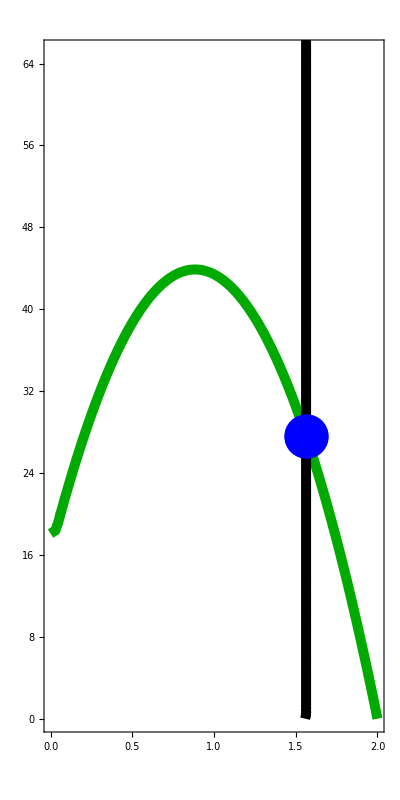

```mathematica
Show[
(*traj,*)
ContourPlot[(dAT2AHp/.{p->solsT2AHp[[5]][[3]][[2]]})==0,{A,0,10},{H,0,150}, PlotPoints->200, ContourStyle->{Darker[Green],Thickness[0.018]}],
ContourPlot[(dHT2AHp/.{p->solsT2AHp[[5]][[3]][[2]]})==0,{A,0,10},{H,0,150}, PlotPoints->200, ContourStyle->{Black,Thickness[0.018]}],
Graphics[{PointSize->0.08,Blue,Point[{solsT2AHp[[5]][[1]][[2]],solsT2AHp[[5]][[2]][[2]]}]}],
PlotRange->{All,{0,65}},AspectRatio->2,LabelStyle->{Black,16}
]
```

### A1F

```mathematica
Clear[ds]
```

```mathematica
solsT2ASI[[1]]/.{ds->0.06,k1->2}
```

{S→26.3662,F→0.,A→0.2225}

```mathematica
DisplayBifurcationDiagram[T2ASI/.{k1->2},ds,MaxSteps->Infinity, MinStepSize->0.1]
$BifurcationDiagramBPs
```

DisplayBifurcationDiagram[DSSetParameters[DynamicalSystem[«3 ODEs»,{A,S,F},{2,ds},{8→8,0.0153→0.0153,0.2314→0.2314,1→1,0.8→0.8,0.0075→0.0075,0.05157→0.05157}],{2→2}],ds,MaxSteps→∞,MinStepSize→0.1]

{BifurcationPoint[Hopf,{0.858323296631137,12.8289035466881,34.7854269752218},{0.0075→0.0075,0.0153→0.0153,0.05157→0.05157,0.2314→0.2314,0.8→0.8,1→1,8→8,ds→0.044646776600161}],BifurcationPoint[Hopf,{0.8843,40.6792970588235,0},{0.0075→0.0075,0.0153→0.0153,0.05157→0.05157,0.2314→0.2314,0.8→0.8,1→1,8→8,ds→0.097013820919602}],BifurcationPoint[Branch,{1.65644073502168,21.1955939647119,0},{0.0075→0.0075,0.0153→0.0153,0.05157→0.05157,0.2314→0.2314,0.8→0.8,1→1,8→8,ds→0.10739695473534}],BifurcationPoint[Branch,{2.00000000011787,0,0},{0.0075→0.0075,0.0153→0.0153,0.05157→0.05157,0.2314→0.2314,0.8→0.8,1→1,8→8,ds→0.109706910461142}]}

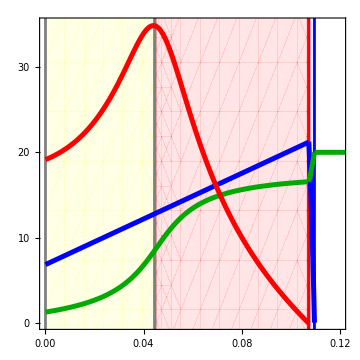

```mathematica
Clear[k1,ds];
k1=2;
P2T2ASI= Show[
RegionPlot[0.1097> x>0.10739,{x,0,0.15},{y,-10,100}, BoundaryStyle->Blue,PlotStyle->{LightBlue}, PlotPoints->100],
RegionPlot[0.10739> x>0.0446,{x,0,0.15},{y,-10,100}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0446> x>-1,{x,0,0.15},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[20,{ds,0.1097 ,0.15}, PlotStyle->{Darker[Green],Thickness[0.01]}],

Plot[Re[solsT2ASI[[4]][[3]][[2]]]*10,{ds,0,0.10739}, PlotStyle->{Darker[Green],Thickness[0.01]},PlotPoints->100],
Plot[Re[solsT2ASI[[4]][[1]][[2]]],{ds,0,0.10739}, PlotStyle->{Blue,Thickness[0.01]}],

Plot[Re[solsT2ASI[[1]][[1]][[2]]],{ds,0.10739,0.1097}, PlotStyle->{Blue,Thickness[0.01]}],
Plot[Re[solsT2ASI[[1]][[3]][[2]]]*10,{ds,0.10739,0.1097}, PlotStyle->{Darker[Green],Thickness[0.01]}],

Plot[Re[solsT2ASI[[4]][[2]][[2]]],{ds,0,0.10739}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16, PlotPoints->200],

PlotRange->{{0,0.12},{0,35}},
Frame->True,
FrameTicks->{{{0,10,20,30},None},{{{0.00,"0.00"},0.02,0.04, 0.06,0.08,{0.10,"0.10"},0.12},None}},
 LabelStyle->{Black,16},ImageSize->Medium
]
```

### A1H

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
FullSimplify[D[r*A*(1 - A/k1)/A,A]]
```

-r/k1

```mathematica
FullSimplify[D[-(f/(h+A))*A*(S+theta*F)/A,A]]
```

(f (S+F theta))/(A+h)^2

```mathematica
SelfLimT2ASI= -r/k1;
C1= (f (solsT2ASI[[4]][[1]][[2]]+solsT2ASI[[4]][[2]][[2]] theta))/(solsT2ASI[[4]][[3]][[2]]+h)^2;
C2= (f solsT2ASI[[1]][[1]][[2]])/(solsT2ASI[[1]][[3]][[2]]+h)^2;
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
r = 1;
theta = 0.8;
```

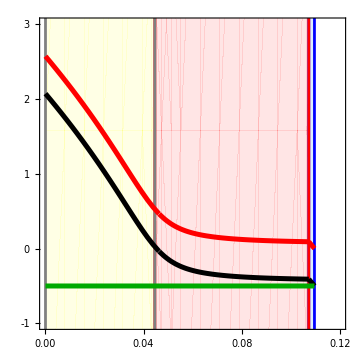

```mathematica
Clear[ds];
k1 = 2;
P4SIZA = Show[
RegionPlot[0.1097> x>0.10739,{x,0,0.15},{y,-10,100}, BoundaryStyle->Blue,PlotStyle->{LightBlue}, PlotPoints->100],
RegionPlot[0.10739> x>0.0446,{x,0,0.15},{y,-10,100}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0446> x>-1,{x,0,0.15},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[C1],{ds,0,0.10739}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimT2ASI] + Re[C1],{ds,0,0.10739}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[C2],{ds,0.10739,0.1097}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimT2ASI] + Re[C2],{ds,0.10739,0.1097}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimT2ASI],{ds,0,0.1097}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,0.12},{-1,3}},
Frame->True,
FrameTicks->{{{-1,0,1,2,3},None},{{{0.00,"0.00"},0.02,0.04, 0.06,0.08,{0.10,"0.10"},0.12},None}}, LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

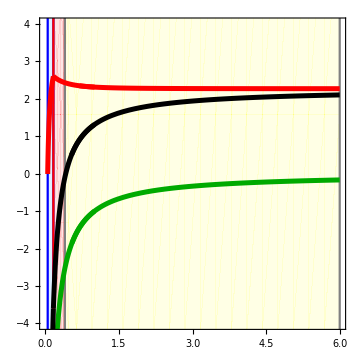

```mathematica
Clear[k1];
ds = 0.02;
P4SIZA = Show[
RegionPlot[0.161> x>0.0451,{x,0,6},{y,-10,100}, BoundaryStyle->Blue,PlotStyle->{LightBlue}, PlotPoints->100],
RegionPlot[0.395> x>0.161,{x,0,6},{y,-10,100}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[6> x>0.395,{x,0,6},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[C1],{k1,0.161,6}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[C1],{k1,0.161,1}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimT2ASI],{k1,0.161,1}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimT2ASI],{k1,0.161,6}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimT2ASI] + Re[C1],{k1,0.161,1}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimT2ASI] + Re[C1],{k1,0.161,6}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[C2],{k1,0.0451,0.161}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimT2ASI] + Re[C2],{k1,0.0451,0.161}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,6},{-4,4}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

### Loop Setup

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
D[f /(A+h),A]
```

-f/(A+h)^2

```mathematica
D[f A^2/(A^2+h^2),A]
```

-(2 A^3 f)/((A^2+h^2)^2)+(2 A f)/(A^2+h^2)

#### Jacobian Elements

```mathematica
J11T2ASI = FullSimplify[D[dAT2ASI,A]];
J12T2ASI = FullSimplify[D[dAT2ASI,S]];
J13T2ASI = FullSimplify[D[dAT2ASI,F]];
J21T2ASI = FullSimplify[D[dST2ASI,A]];
J22T2ASI = FullSimplify[D[dST2ASI,S]];
J23T2ASI = FullSimplify[D[dST2ASI,F]];
J31T2ASI = FullSimplify[D[dFT2ASI,A]];
J32T2ASI = FullSimplify[D[dFT2ASI,S]];
J33T2ASI = FullSimplify[D[dFT2ASI,F]];
```

```mathematica
JMT2ASI= {{J11T2ASI,J12T2ASI,J13T2ASI},{J21T2ASI,J22T2ASI,J23T2ASI},{J31T2ASI,J32T2ASI,J33T2ASI}};
JMT2ASI= JMT2ASI//MatrixForm
```

(r-(2 A r)/k1-(f h (S+F theta))/(A+h)^2 | -(A f)/(A+h) | -(A f theta)/(A+h)
(e f h (S+F theta))/(A+h)^2 | -ds+(A e f)/(A+h)-F u | (A e f theta)/(A+h)-S u
0 | F u | -ds+S u-v)

```mathematica
DJac = {{jAA,jAS,jAF},{jSA,jSS,jSF},{0,jFS,jFF}};
DJac//MatrixForm
```

(jAA | jAS | jAF
jSA | jSS | jSF
0 | jFS | jFF)

```mathematica
CharacteristicPolynomial[DJac,x]
```

-jFS (-jAF jSA+jAA jSF-jSF x)+(jFF-x) (-jAS jSA+jAA jSS-jAA x-jSS x+x^2)

```mathematica
Det[DJac]
```

-jFZ jSS jZF+jFS jSZ jZF-jFS jSF jZZ+jFF jSS jZZ

#### Feedbacks & Oscillation Criterion

```mathematica
T2ASIL1 = FullSimplify[(J11T2ASI+J22T2ASI+J33T2ASI)];
T2ASIL2 = FullSimplify[(J12T2ASI*J21T2ASI-J11T2ASI*J22T2ASI)+(-J11T2ASI*J33T2ASI)+(J23T2ASI*J32T2ASI-J22T2ASI*J33T2ASI)];
T2ASIL3= -J12T2ASI J33T2ASI J21T2ASI+J13T2ASI J32T2ASI J21T2ASI-J11T2ASI J32T2ASI J23T2ASI +J11T2ASI J22T2ASI J33T2ASI;
OCT2ASI = (T2ASIL1 T2ASIL2)+T2ASIL3;
```

### Loop Plots (F3)

```mathematica
Clear[k1,ds]
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 0.8;
r = 1;
```

#### F3A (Upper v. Lower)

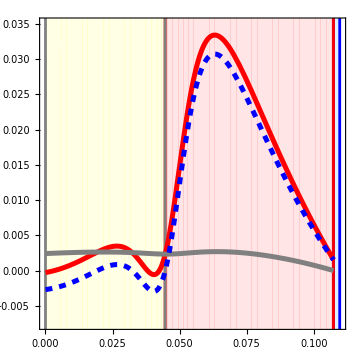

```mathematica
k1=2;
Show[
RegionPlot[0.1097> x>0.10739,{x,0,0.15},{y,-10,100}, BoundaryStyle->Blue,PlotStyle->{LightBlue}, PlotPoints->100],
RegionPlot[0.10739> x>0.0446,{x,0,0.15},{y,-10,100}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0446> x>-1,{x,0,0.15},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[T2ASIL1 * T2ASIL2/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Red,Thickness[0.01]}],

Plot[Re[-T2ASIL3/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[OCT2ASI/.solsT2ASI[[4]],{ds,0,0.10739}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{All,{-0.0075,0.035}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### F3B (F1 v. F2)

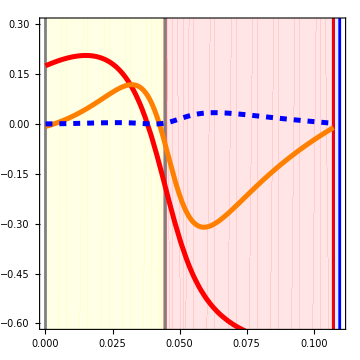

```mathematica
Show[
RegionPlot[0.1097> x>0.10739,{x,0,0.15},{y,-10,100}, BoundaryStyle->Blue,PlotStyle->{LightBlue}, PlotPoints->100],
RegionPlot[0.10739> x>0.0446,{x,0,0.15},{y,-10,100}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0446> x>-1,{x,0,0.15},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[T2ASIL1/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Red,Thickness[0.01]}],

Plot[Re[T2ASIL2*5/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Orange,Thickness[0.01]}],

Plot[Re[T2ASIL1 * T2ASIL2/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{All,{-0.6,0.3}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### F3C (F1)

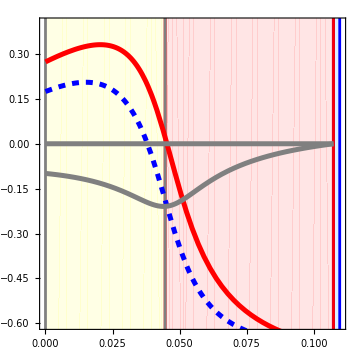

```mathematica
Show[
RegionPlot[0.1097> x>0.10739,{x,0,0.15},{y,-10,100}, BoundaryStyle->Blue,PlotStyle->{LightBlue}, PlotPoints->100],
RegionPlot[0.10739> x>0.0446,{x,0,0.15},{y,-10,100}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0446> x>-1,{x,0,0.15},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[T2ASIL1/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

Plot[Re[J11T2ASI/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[J22T2ASI/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[J33T2ASI/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Gray,Thickness[0.01]}],

PlotRange->{All,{-0.6,0.4}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### F3D (F2)

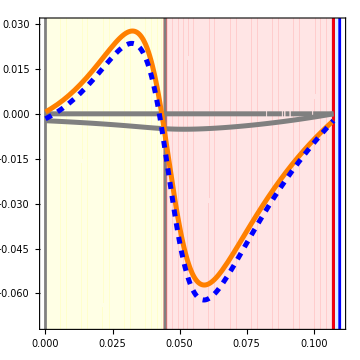

```mathematica
Show[
RegionPlot[0.1097> x>0.10739,{x,0,0.15},{y,-10,100}, BoundaryStyle->Blue,PlotStyle->{LightBlue}, PlotPoints->100],
RegionPlot[0.10739> x>0.0446,{x,0,0.15},{y,-10,100}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0446> x>-1,{x,0,0.15},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[(-J11T2ASI*J33T2ASI)/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Gray,Thickness[0.01]},PlotPoints->220],
Plot[Re[(J23T2ASI*J32T2ASI-J22T2ASI*J33T2ASI)/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Gray,Thickness[0.01]},PlotPoints->200],
Plot[Re[(J12T2ASI*J21T2ASI-J11T2ASI*J22T2ASI)/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Orange,Thickness[0.01]}],
Plot[Re[T2ASIL2/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{All,{-0.07,0.03}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### F3E

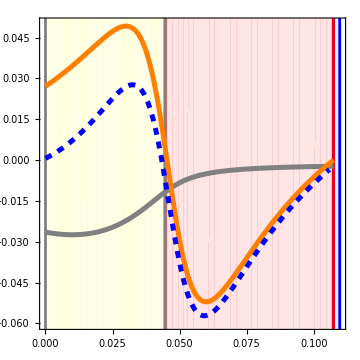

```mathematica
Show[
RegionPlot[0.1097> x>0.10739,{x,0,0.15},{y,-10,100}, BoundaryStyle->Blue,PlotStyle->{LightBlue}, PlotPoints->100],
RegionPlot[0.10739> x>0.0446,{x,0,0.15},{y,-10,100}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0446> x>-1,{x,0,0.15},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[(J12T2ASI*J21T2ASI)/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J11T2ASI*J22T2ASI)/.solsT2ASI[[4]]],{ds,0,0.10739}, PlotStyle->{Orange,Thickness[0.01]}],
Plot[Re[(J12T2ASI*J21T2ASI-J11T2ASI*J22T2ASI)/.solsT2ASI[[4]]],{ds,0,0.1059}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],


PlotRange->{All,{-0.06,0.05}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```